```mathematica
(*@Return {cleanedDat, its length, its min time, its max time}: a cleaned, sorted data list of elements of time*)
cleanRawData[rawData_]:=Module[
{dat},
dat=Select[rawData,#[[1]]<40000&];
dat=#[[1]]&/@dat;
dat=Sort[dat];
{dat, Length[dat],Min[dat],Max[dat]}
];
```

```mathematica
(*This is almost the same function as above (which is legacy code so can only be found in muon_play.nb.), except that we can choose the starting time delimter and the
ending time delimiter. Therefore it can somehow be more flexible.
Return: {distList, binWdith, numBin}*)
```

```mathematica
getDist[data_,startTime_, endTime_,numBin_]:=Module[
{binWidth,hisDat,delimits,counts,trueEndTime,trueStartTime, distList,i,lenCounts},

(*This expression ensures that the endTime will always be binned.*)
binWidth=Ceiling[(endTime-startTime+1)/numBin];

(*Now I want to determine the true suitable endTime given the bin width.
Therefore, we will always guarantee to have the number of bins as initially intended.
Therefore, this function should always function exactly the same as the previous one,
when startTime was set to be Min[data].*)
trueStartTime=startTime;
If[Mod[endTime - startTime,binWidth]==0,
trueEndTime=endTime,
trueEndTime=startTime+binWidth*numBin];

hisDat= HistogramList[data,{trueStartTime,trueEndTime,binWidth}];
delimits=hisDat[[1]];
counts=hisDat[[2]];
lenCounts=Length[counts];
(*Print[lenCounts];*)

(*Now we want to settle delimits and counts into a distribution list of element {startTime, numCounts}*)
distList={};
(*Print["Hey"];
Print[i];
Print[Length[counts]];*)
For[i=1,i≤lenCounts,i++,
(*Print[i];*)
AppendTo[distList,{delimits[[i]],counts[[i]]}];
(*Print[i,": ",distList];*)
];
{distList, binWidth,numBin}
]
```

```mathematica
(*Obtain the estimated error from an experimental value*)
getErr[count_]:=√count;
```

```mathematica
(*Similar to getLogList except that we only get the original count districution instead of log of count.*)
getDistList[cleanData_,startTime_,endTime_, numBin_]:=Module[
{truncDist,binWidth,errList},

(*truncDist is a distribution list of {time, counts} that truncates some early times and late times.*)
{truncDist,binWidth}=getDist[cleanData,startTime, endTime,numBin][[1;;2]];

(*Obtain the error list for truncDist*)
errList={#[[1]],getErr@#[[2]]}&/@truncDist;

{truncDist,binWidth,errList}
];
```

```mathematica
(*@return {truncDist, binWidth, logErrList}
truncDist: a list of {time, Log[counts]} for all times starting from startTime and ending before endTime
logErrList: a list of errors for truncDist, with elements of {time, logError}*)

getLogList[cleanData_,startTime_,endTime_, numBin_]:=Module[
{truncDist,binWidth,errList},

(*truncDist is a distribution list of {time, counts} that truncates some early times and late times.*)
{truncDist,binWidth}=getDist[cleanData,startTime, endTime,numBin][[1;;2]];

(*Obtain the error list for the log of truncDist.
Notice that, since we use the getErr function direction on the original count, this getErr@#[[2]] can be
zero when the count is zero. Therefore, the log error will be 0 as a result. This will not be able
to take reciprocal and produce a weight. Therefore, we must avoid this type of process.*)
errList={#[[1]],Log[1+(getErr@#[[2]])/If[#[[2]]==0,1,#[[2]]]]}&/@truncDist;
truncDist={#[[1]],Log@#[[2]]}&/@truncDist;

{truncDist,binWidth,errList}
];
```

```mathematica
(*@Return: a log list truncating noise before the start trunc time and after the end trunc time as
well as the corresponding truncated error list.*)
truncLogList[logList_,errList_,startTruncTime_,endTruncTime_]:=Module[
{truncList,truncErrList},

truncList=Select[logList,startTruncTime≤#[[1]]≤endTruncTime&];
truncErrList=Select[errList,startTruncTime≤#[[1]]≤endTruncTime&];

{truncList,truncErrList}
];
```

```mathematica
getWeights[errList_]:=1/(If[#[[2]]==0,∞,#[[2]]]&/@errList)^2;
```

```mathematica
(*Obtain the weighted linear fit model from intial set up.
Notice that, when using this function, we must set startTime and endTime properly so that
we can avoid bins in which there are zero counts. If this happened, then the corresponding 
log error will be zero and thus inverting the log error to get weight will run into problem.

@return {estimated lifetime, the function form -λ*t+b, width of the bin}*)
getFitModel[cleanData_,startTime_,endTime_, numBin_,x_,needWeight_:True]:=Module[
{logDat,width,errDat,lm,t,λ,lifeTime},

(*First we obtain our logDat and errList.*)
{logDat,width,errDat}=getLogList[cleanData,startTime,endTime,numBin];

(*Then we just directly fit our data.*)
lm=LinearModelFit[logDat,t,t,Weights-> If[needWeight,getWeights[errDat],Automatic],VarianceEstimatorFunction->(1&)];
λ=-lm["BestFitParameters"][[2]];
lifeTime=1/λ;

{lifeTime,Normal[lm]/.t-> x,width}
];
```

```mathematica
getNonlinearFit[cleanData_,startTime_,endTime_, numBin_,x_,needWeight_:True]:=Module[
{dat,width,errDat,nlm,a,b,τ,t,lifeTime},

(*First we obtain our logDat and errList.*)
{dat,width,errDat}=getDistList[cleanData,startTime,endTime,numBin];

(*Then we just directly fit our data.*)
nlm=NonlinearModelFit[dat,{a ⅇ^(-t/τ)+b,{10000>a>0,10>b>0,1000<τ<3000}},{a,τ,b},t,Weights->If[needWeight,getWeights[errDat],Automatic],VarianceEstimatorFunction->(1&)];
τ=τ/.nlm["BestFitParameters"][[2]];
lifeTime=τ;

{lifeTime,Normal[nlm]/.t-> x,width}
];
```

```mathematica
(*All the code above are pre-defined functions.*)
```

```mathematica
mdat=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",1,Range[1,12920],1}];
```

```mathematica
mdat1=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",2,Range[1,2769],1}];
```

```mathematica
mdat2=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",3,Range[1,1299],1}];
```

```mathematica
mdat3=Import["/Users/benxgh1996/Desktop/Muon/muon_dat.xlsx",{"Data",4,Range[1,8852],1}];
```

```mathematica
{Min[mdat],Max[mdat]}
```

{40.,19880.}

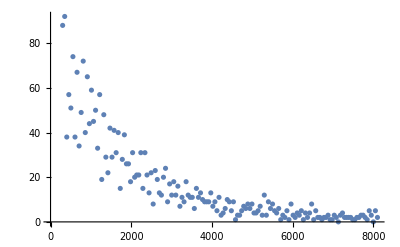

{1566.28,1.01414+78.0304 ⅇ^(-0.000638454 x),51}

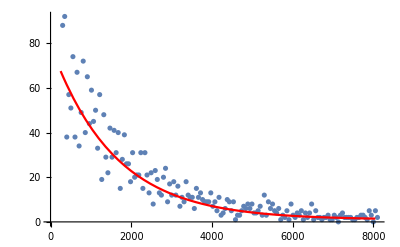

```mathematica
(*mdat*)
{startTime,endTime,binWidth}={300,8000,50};
dat=mdat;
ListPlot[Tooltip[getDistList[dat,startTime,endTime,(endTime-startTime)/binWidth][[1]]]]
nlm=getNonlinearFit[dat,startTime,endTime,(endTime-startTime)/binWidth,x]
Show[ListPlot[Tooltip@getDistList[dat,startTime,endTime,(endTime-startTime)/binWidth][[1]]],Plot[nlm[[2]],{x,startTime-binWidth, endTime+binWidth},PlotStyle->Red,PlotRange->Full]]
```

```mathematica
{startTime,endTime,binWidth}={300,6200,50};
dist=getDistList[mdat,startTime,endTime,(endTime-startTime)/binWidth][[1]];
Manipulate[Show[ListPlot[dist,PlotStyle->Red],Plot[a ⅇ^(-t/τ)+b,{t,startTime,endTime}]],{a,0,1000,Appearance-> "Labeled"},{b,0,5,Appearance-> "Labeled"},{τ,1000,3000,Appearance-> "Labeled"}]
```

```mathematica
Manipulate[Plot[a ⅇ^(-t/τ),{t,0,6000}],{a,1,10000,Appearance-> "Labeled"},{τ,1000,3000,Appearance-> "Labeled"}]
```

```mathematica
{Min[mdat],Max[mdat],Length[mdat]}
```

{40.,19880.,12920}

```mathematica
{startTime,endTime,binWidth}={300,5000,50}
getNonlinearFit[mdat,startTime,endTime,(endTime-startTime)/binWidth,x,False]
```

{300,5000,600}

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]} is not a list of real numbers with dimensions {7} at {a$196568,λ$196568,b$196568} = {-2.13387×10^132,-1.24977×10^130,57.8333}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of λ$196568→-1.24977×10^130.

{lifeTime$196568,57.8333-2.13387×10^132 ⅇ^(1.24977×10^130 x),601}

{300,6000,100}

{1505.32,5.24252-0.000664312 x,101}

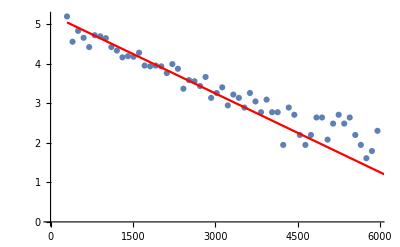

```mathematica
(*mdat*)
{startTime,endTime,binWidth}={300,6000,100}
lm=getFitModel[mdat,startTime,endTime,(endTime-startTime)/binWidth,x,True]
(*ListPlot[Tooltip@getLogList[mdat,startTime,endTime,(endTime-startTime)/binWidth][[1]]]*)
Show[ListPlot[Tooltip@getLogList[mdat,startTime,endTime,(endTime-startTime)/binWidth][[1]]],Plot[lm[[2]],{x,startTime, endTime+binWidth},PlotStyle->Red]]
```

{100,6200,400}

{2085.76,4.80055-0.000479441 x,401}

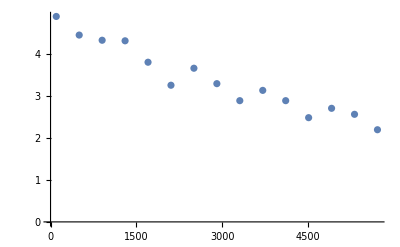

```mathematica
(*mdat1*)
{startTime,endTime,binWidth}={100,6200,400}
getFitModel[mdat1,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat1,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
```

{600,9000,600}

{2410.75,4.7609-0.000414808 x,601}

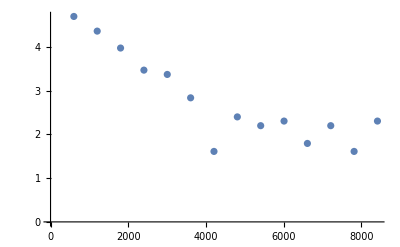

```mathematica
(*mdat2*)
{startTime,endTime,binWidth}={600,9000,600}
getFitModel[mdat2,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat2,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
(*getLogList[mdat2,startTime,endTime,(endTime-startTime)/50][[1]]*)
```

19880.

{0,3000,50}

{337.867,8.02391-0.00295975 x,51}

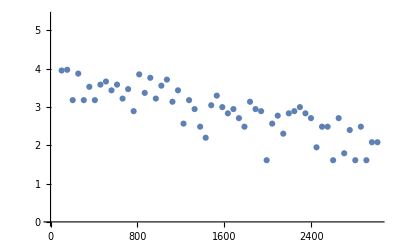

```mathematica
(*mdat3*)
Max[mdat3]
{startTime,endTime,binWidth}={0,3000,50}
getFitModel[mdat3,startTime,endTime,(endTime-startTime)/binWidth,x]
ListPlot[Tooltip@getLogList[mdat3,startTime,endTime,(endTime-startTime)/binWidth][[1]]]
```